```mathematica
SetDirectory["/home/s1220054/Dissertation/Dissertation/DiSamp/src"]
```

/home/s1220054/Dissertation/Dissertation/DiSamp/src

```mathematica
typelist=Table[Import["type_"<>ToString[i]<>".txt","CSV"],{i,20}]
```

{{{0,0},{163,345},{163,346},{164,345},{164,346},{165,345},{165,346},{165,347},{166,344},{166,345},{166,346},{167,344},{167,345},{167,346},{167,347},{168,341},{168,342},{168,343},{168,344},{168,345},{168,346},{168,347},{168,348},{168,349},{169,333},{169,341},{169,342},{169,343},{169,344},{169,345},{169,346},{169,347},{169,348},{169,349},{170,331},{170,333},{170,341},{170,342},{170,343},{170,344},{170,345},{170,346},{170,347},{170,348},{171,330},{171,331},{171,332},{171,333},{171,340},{171,341},{171,342},{171,343},{171,344},{171,345},{171,346},{171,347},{171,348},{172,328},{172,329},{172,330},{172,331},{172,332},30685,{493,280},{493,281},{493,282},{493,283},{493,284},{493,285},{493,286},{493,287},{493,288},{493,289},{493,290},{493,291},{493,292},{493,293},{494,278},{494,279},{494,280},{494,281},{494,282},{494,283},{494,284},{494,285},{494,286},{494,287},{494,288},{494,289},{494,290},{494,291},{494,292},{494,293},{495,278},{495,279},{495,280},{495,281},{495,282},{495,283},{495,284},{495,285},{495,286},{495,287},{495,288},{495,290},{496,279},{496,280},{496,281},{496,282},{496,283},{496,284},{496,285},{496,286},{496,287},{496,288},{497,281},{497,282},{497,283},{497,284},{497,285},{498,279},{498,280},{498,281},{498,282},{498,283}},18,{1}}
 |  |  |  |

```mathematica
typelist[[1]]
```

{{0,0},{163,345},{163,346},{164,345},{164,346},{165,345},{165,346},{165,347},{166,344},{166,345},{166,346},{167,344},{167,345},{167,346},{167,347},{168,341},{168,342},{168,343},{168,344},{168,345},{168,346},{168,347},{168,348},{168,349},{169,333},{169,341},{169,342},{169,343},{169,344},{169,345},{169,346},{169,347},{169,348},{169,349},{170,331},{170,333},{170,341},{170,342},{170,343},{170,344},{170,345},{170,346},{170,347},{170,348},{171,330},{171,331},{171,332},{171,333},{171,340},{171,341},{171,342},{171,343},{171,344},{171,345},{171,346},{171,347},{171,348},{172,328},{172,329},{172,330},{172,331},{172,332},{172,333},30683,{493,279},{493,280},{493,281},{493,282},{493,283},{493,284},{493,285},{493,286},{493,287},{493,288},{493,289},{493,290},{493,291},{493,292},{493,293},{494,278},{494,279},{494,280},{494,281},{494,282},{494,283},{494,284},{494,285},{494,286},{494,287},{494,288},{494,289},{494,290},{494,291},{494,292},{494,293},{495,278},{495,279},{495,280},{495,281},{495,282},{495,283},{495,284},{495,285},{495,286},{495,287},{495,288},{495,290},{496,279},{496,280},{496,281},{496,282},{496,283},{496,284},{496,285},{496,286},{496,287},{496,288},{497,281},{497,282},{497,283},{497,284},{497,285},{498,279},{498,280},{498,281},{498,282},{498,283}}
 |  |  |  |

```mathematica
typelist[[2]]
```

{{0,0},{360,351},{361,351},{361,352},{362,350},{362,351},{362,352},{362,353},{363,351},{363,352},{364,351},{364,352},{365,351},{365,352},{366,352},{367,352}}

```mathematica
typelist[[3]]
```

{{0,0},{353,339},{354,333},{354,334},{354,335},{354,336},{354,337},{354,338},{354,339},{355,333},{355,336},{355,337},{355,338},{355,339},{356,330},{356,331},{356,332},{356,333},{356,336},{356,337},{356,338},{356,339},{357,333},{357,336},{357,337},{357,338},{358,337},{359,336},{359,337},{360,336},{360,337},{360,338},{361,336},{361,337}}

```mathematica
typelist[[9]]
```

{{0,0},{355,334},{355,335},{356,334},{356,335},{357,330},{357,331},{357,332},{357,334},{357,335},{358,329},{358,330},{358,331},{358,332},{358,333},{358,334},{358,335},{358,336},{359,328},{359,329},{359,330},{359,331},{359,332},{359,333},{359,334},{359,335},{360,328},{360,329},{360,330},{360,331},{360,332},{360,333},{360,334},{360,335},{361,326},{361,327},{361,329},{361,330},{361,331},{361,332},{361,333},{361,334},{361,335},{362,322},{362,323},{362,324},{362,325},{362,326},{362,327},{362,328},{362,329},{362,330},{362,331},{362,332},{362,333},{362,334},{362,335},{362,336},{362,337},{363,321},{363,322},{363,323},{363,324},{363,325},{363,326},{363,327},{363,328},{363,329},{363,330},{363,331},{363,332},{363,333},{363,334},{363,335},{364,319},{364,320},{364,321},{364,322},{364,323},{364,324},{364,325},{364,326},{364,327},{364,328},{364,329},{364,330},{364,333},{364,334},{365,319},{365,320},{365,321},{365,322},{365,323},{365,324},{365,325},{365,326},{365,327},{365,328},{365,329},{366,312},{366,313},{366,314},{366,318},{366,319},{366,320},{366,321},{366,322},{366,323},{366,324},{366,325},{366,327},{366,328},{366,329},{367,312},{367,313},{367,314},{367,315},{367,316},{367,317},{367,318},{367,319},{367,320},{367,321},{367,322},{367,323},{367,324},{367,325},{367,326},{367,327},{368,308},{368,309},{368,310},{368,311},{368,312},{368,313},{368,314},{368,315},{368,316},{368,317},{368,318},{368,319},{368,320},{368,321},{368,322},{368,323},{368,324},{368,325},{368,326},{368,327},{368,328},{369,304},{369,305},{369,306},{369,307},{369,308},{369,309},{369,310},{369,311},{369,312},{369,313},{369,314},{369,315},{369,316},{369,317},{369,318},{369,319},{369,320},{369,321},{369,322},{369,323},{369,324},{369,325},{369,326},{369,327},{369,328},{370,303},{370,304},{370,305},{370,306},{370,307},{370,308},{370,309},{370,310},{370,311},{370,312},{370,313},{370,314},{370,315},{370,316},{370,319},{370,320},{370,321},{370,322},{370,323},{370,324},{370,325},{370,326},{370,327},{370,328},{371,303},{371,304},{371,305},{371,306},{371,307},{371,308},{371,309},{371,310},{371,311},{371,312},{371,313},{371,314},{371,315},{371,318},{371,319},{371,320},{371,321},{371,322},{371,323},{371,324},{371,325},{371,326},{371,327},{371,328},{372,303},{372,304},{372,305},{372,306},{372,307},{372,308},{372,309},{372,310},{372,311},{372,312},{372,313},{372,314},{372,315},{372,316},{372,317},{372,318},{372,320},{372,321},{372,322},{372,323},{372,324},{372,325},{372,326},{372,327},{372,328},{373,296},{373,297},{373,304},{373,305},{373,306},{373,307},{373,308},{373,309},{373,310},{373,311},{373,312},{373,313},{373,314},{373,315},{373,316},{373,317},{373,320},{373,321},{373,322},{373,323},{373,324},{373,325},{373,326},{373,327},{373,328},{374,285},{374,294},{374,295},{374,296},{374,297},{374,298},{374,299},{374,300},{374,301},{374,302},{374,303},{374,304},{374,305},{374,306},{374,307},{374,308},{374,309},{374,310},{374,311},{374,316},{374,320},{374,321},{374,322},{374,323},{374,324},{374,325},{374,326},{374,327},{374,328},{375,274},{375,275},{375,276},{375,277},{375,278},{375,279},{375,280},{375,282},{375,283},{375,284},{375,285},{375,288},{375,289},{375,290},{375,295},{375,296},{375,297},{375,298},{375,299},{375,300},{375,301},{375,302},{375,303},{375,304},{375,305},{375,306},{375,307},{375,308},{375,309},{375,310},{375,311},{375,319},{375,320},{375,321},{375,322},{375,323},{375,324},{375,325},{375,326},{375,327},{375,328},{376,274},{376,275},{376,276},{376,277},{376,278},{376,279},{376,280},{376,281},{376,282},{376,283},{376,284},{376,285},{376,288},{376,289},{376,290},{376,291},{376,292},{376,293},{376,294},{376,295},{376,296},{376,297},{376,298},{376,299},{376,300},{376,301},{376,302},{376,303},{376,304},{376,305},{376,306},{376,307},{376,308},{376,309},{376,310},{376,311},{376,319},{376,320},{376,321},{376,322},{376,323},{376,324},{376,325},{376,328},{377,274},{377,275},{377,276},{377,277},{377,278},{377,279},{377,280},{377,281},{377,282},{377,283},{377,284},{377,285},{377,286},{377,288},{377,289},{377,292},{377,293},{377,294},{377,295},{377,296},{377,297},{377,298},{377,299},{377,300},{377,301},{377,302},{377,303},{377,304},{377,305},{377,306},{377,307},{377,308},{377,309},{377,310},{377,311},{377,319},{377,320},{377,321},{377,322},{377,323},{377,324},{377,325},{378,274},{378,275},{378,276},{378,277},{378,278},{378,279},{378,280},{378,281},{378,282},{378,283},{378,284},{378,285},{378,286},{378,293},{378,294},{378,295},{378,296},{378,297},{378,298},{378,299},{378,300},{378,301},{378,302},{378,303},{378,304},{378,305},{378,306},{378,307},{378,308},{378,309},{378,310},{378,311},{378,318},{378,319},{378,320},{378,321},{378,322},{378,323},{378,324},{378,325},{378,326},{379,271},{379,272},{379,273},{379,274},{379,275},{379,276},{379,277},{379,278},{379,279},{379,280},{379,281},{379,282},{379,283},{379,284},{379,285},{379,286},{379,287},{379,293},{379,294},{379,295},{379,296},{379,297},{379,298},{379,299},{379,300},{379,301},{379,302},{379,303},{379,304},{379,305},{379,306},{379,307},{379,308},{379,309},{379,310},{379,311},{379,312},{379,313},{379,318},{379,319},{379,320},{379,321},{379,322},{379,323},{379,324},{380,270},{380,271},{380,272},{380,273},{380,274},{380,275},{380,276},{380,277},{380,278},{380,279},{380,280},{380,281},{380,282},{380,283},{380,284},{380,285},{380,286},{380,287},{380,288},{380,289},{380,292},{380,293},{380,294},{380,295},{380,296},{380,297},{380,298},{380,299},{380,300},{380,301},{380,302},{380,303},{380,304},{380,308},{380,309},{380,310},{380,311},{380,312},{380,313},{380,314},{380,315},{380,316},{380,317},{380,318},{380,319},{380,320},{380,321},{380,322},{380,323},{381,272},{381,273},{381,274},{381,275},{381,276},{381,277},{381,278},{381,279},{381,280},{381,281},{381,282},{381,283},{381,284},{381,285},{381,286},{381,287},{381,288},{381,289},{381,290},{381,291},{381,292},{381,293},{381,294},{381,295},{381,296},{381,297},{381,298},{381,299},{381,300},{381,308},{381,309},{381,310},{381,311},{381,312},{381,313},{381,314},{381,315},{381,316},{381,317},{381,318},{381,319},{381,320},{381,321},{381,322},{381,323},{382,273},{382,274},{382,275},{382,276},{382,277},{382,278},{382,279},{382,280},{382,281},{382,282},{382,283},{382,284},{382,285},{382,286},{382,287},{382,288},{382,289},{382,290},{382,291},{382,292},{382,293},{382,294},{382,295},{382,296},{382,297},{382,298},{382,299},{382,300},{382,308},{382,309},{382,310},{382,311},{382,312},{382,313},{382,314},{382,315},{382,316},{382,317},{382,318},{382,319},{383,272},{383,273},{383,274},{383,275},{383,276},{383,277},{383,278},{383,279},{383,280},{383,281},{383,282},{383,283},{383,284},{383,285},{383,286},{383,287},{383,288},{383,289},{383,290},{383,291},{383,292},{383,293},{383,294},{383,295},{383,296},{383,297},{383,298},{383,299},{383,300},{383,304},{383,305},{383,306},{383,307},{383,308},{383,309},{383,310},{383,311},{383,312},{383,313},{383,314},{383,315},{383,316},{383,317},{383,318},{383,319},{383,320},{384,272},{384,273},{384,274},{384,275},{384,276},{384,277},{384,278},{384,279},{384,280},{384,281},{384,282},{384,283},{384,284},{384,285},{384,286},{384,287},{384,288},{384,289},{384,290},{384,291},{384,292},{384,293},{384,294},{384,295},{384,296},{384,297},{384,298},{384,299},{384,300},{384,303},{384,304},{384,305},{384,306},{384,307},{384,308},{384,309},{384,310},{384,311},{384,312},{384,313},{384,314},{384,315},{384,316},{384,317},{384,318},{385,272},{385,273},{385,274},{385,275},{385,276},{385,277},{385,278},{385,279},{385,280},{385,281},{385,282},{385,283},{385,284},{385,285},{385,286},{385,287},{385,288},{385,289},{385,290},{385,291},{385,292},{385,293},{385,295},{385,296},{385,303},{385,304},{385,305},{385,306},{385,307},{385,308},{385,309},{385,310},{385,311},{385,312},{385,313},{385,314},{385,315},{385,316},{385,317},{385,318},{386,273},{386,274},{386,275},{386,276},{386,278},{386,279},{386,280},{386,281},{386,282},{386,283},{386,284},{386,285},{386,286},{386,287},{386,289},{386,290},{386,291},{386,303},{386,304},{386,305},{386,306},{386,307},{386,308},{386,309},{386,310},{386,311},{386,312},{386,313},{386,314},{386,315},{386,316},{386,317},{387,275},{387,276},{387,281},{387,282},{387,283},{387,284},{387,285},{387,286},{387,291},{387,303},{387,304},{387,305},{387,306},{387,307},{387,308},{387,309},{387,310},{387,311},{387,312},{387,313},{387,314},{387,315},{387,316},{387,317},{388,281},{388,282},{388,283},{388,284},{388,285},{388,291},{388,303},{388,304},{388,305},{388,306},{388,307},{388,308},{388,310},{388,311},{388,312},{388,313},{388,314},{389,303},{389,304},{389,305},{389,306},{389,307},{389,308},{389,309},{389,310},{389,311},{389,312},{389,313},{389,314},{390,303},{390,304},{390,305},{390,306},{390,307},{390,308},{390,309},{390,310},{390,311},{390,312},{391,304},{391,305},{391,306},{391,307},{391,308},{391,309},{391,310},{391,311},{392,300},{392,301},{392,302},{392,303},{392,304},{392,305},{392,306},{392,307},{392,308},{392,309},{393,300},{393,301},{393,302},{393,303},{393,304},{393,305},{393,306},{393,307},{393,308},{393,309},{394,300},{394,301},{394,302},{394,303},{394,304},{394,305},{394,306},{395,300},{395,301},{395,302},{395,303},{396,300},{396,301},{396,302}}

```mathematica
typelist[[12]]
```

{{0,0},{369,342},{369,343},{370,342},{370,343},{370,344},{371,341},{371,342},{371,343},{371,344},{372,341},{372,342},{372,343},{372,344},{373,340},{373,341},{373,342},{373,343},{374,340},{374,341},{374,342},{375,339},{375,340},{375,341},{375,342},{376,339},{376,340},{376,341},{376,342},{377,339},{377,340},{377,341},{377,342},{377,343},{377,344},{378,339},{378,340},{378,341},{378,342},{378,343},{378,344},{378,345},{379,339},{379,340},{379,341},{379,342},{379,343},{379,344},{379,345},{380,339},{380,340},{380,341},{380,342},{380,343},{380,344},{380,345},{381,338},{381,339},{381,340},{381,341},{381,342},{381,343},{381,344},{381,345},{382,341},{382,342},{382,343},{382,344},{382,345},{383,340},{383,341},{383,342},{383,343},{383,344},{383,345},{384,340},{384,341},{384,342},{384,343},{384,344},{385,343},{385,344},{386,344},{386,345},{387,343},{387,344},{387,345},{388,343},{388,344},{388,345},{389,344},{389,345},{390,344},{390,345}}

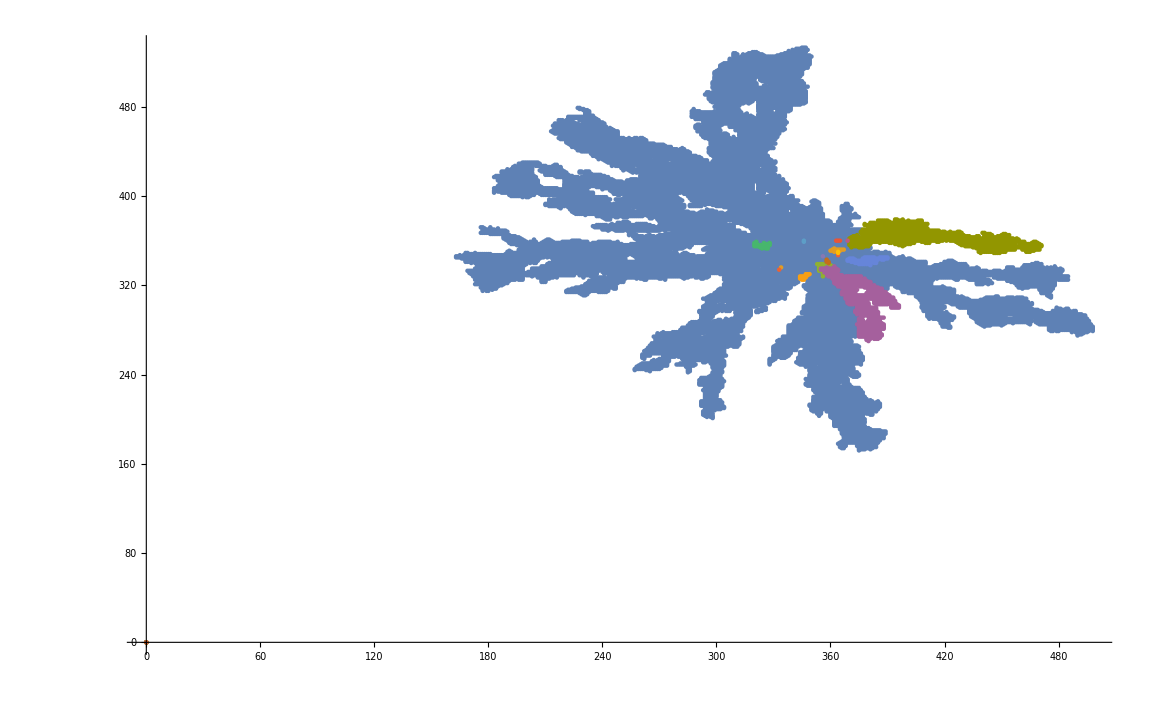

Part::partw: Part 3 of {0, 0} does not exist.

```mathematica
ListPlot[{typelist[[1]],typelist[[2]],typelist[[3]],typelist[[4]],typelist[[5]],typelist[[6]],typelist[[7]],typelist[[8]],typelist[[9]],typelist[[10]],typelist[[11]], typelist[[12]], typelist[[13]], typelist[[14]], typelist[[15]], typelist[[16]], typelist[[17]], typelist[[18]], typelist[[19]]}]
```

```mathematica
data =Import["xi.txt", "CSV"]
```

{{0,11},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0}}

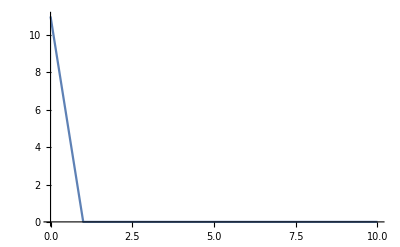

```mathematica
ListLinePlot[data]
```

```mathematica
datanew=Import["array.txt", "CSV"]
```

{1}
 |  |  |  |

```mathematica
ArrayPlot[datanew]
```

-Graphics-